# Mikrofonien viiveet 2 kpl

```mathematica
Remove["`*"]
```

Remove::rmnsm: There are no symbols matching "`*".

```mathematica
v=343;
d=0.2;
l=1;
mic1={0,-d/2};
mic2={0,d/2};
```

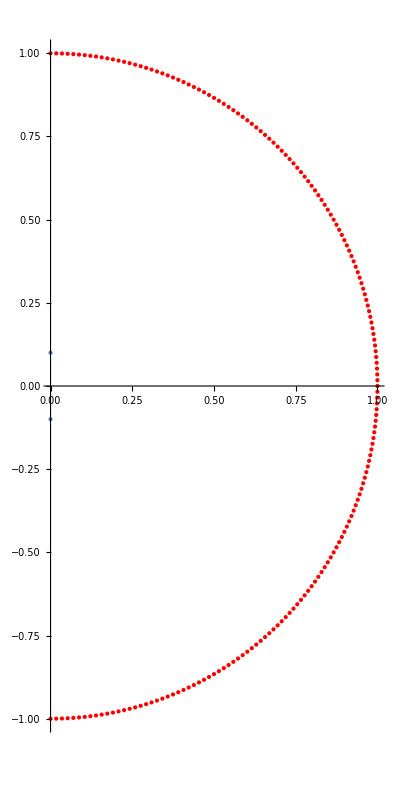

```mathematica
n=181;
src=CirclePoints[{l,-π/2},2 (n-1)][[1;;n]];
Show[ListPlot[{mic1,mic2},PlotStyle->PointSize[Large]],ListPlot[src,PlotStyle->{PointSize[Large],Red}],PlotRange->Full,AspectRatio->2]
```

```mathematica
comp[s_,m1_,m2_]:=EuclideanDistance[s,m1]>EuclideanDistance[s,m2];
diff[s_,m1_,m2_]:=EuclideanDistance[s,m1]-EuclideanDistance[s,m2]
distances=Reap[For[i=1,i<=n,i++,
Which[comp[src[[i]],mic1,mic2],Sow[{0,diff[src[[i]],mic1,mic2]}],
comp[src[[i]],mic2,mic1],Sow[{diff[src[[i]],mic2,mic1],0}],
True,Sow[{0,0}]]]][[2,1]];
delays=distances/v;
```

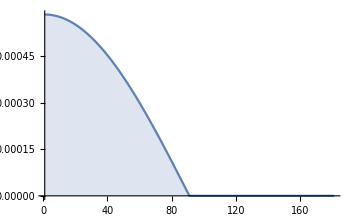

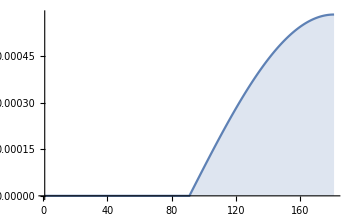

```mathematica
DiscretePlot[delays[[All,1]][[k]],{k,1,n}]
DiscretePlot[delays[[All,2]][[k]],{k,1,n}]
```

```mathematica
div=Round[(n+1)/2];

expr1=a1 Cos[b1( x-1)];
pars1=FindFit[delays[[All,1]][[;;div]],{expr1,a1>=0,b1>=0},{{a1,0},{b1,0.5}},x,Method->{"NMinimize",Method->"DifferentialEvolution"}];
fun1=Piecewise[{{expr1/.pars1,div>=x>=1}},0]

fun2=Piecewise[{{expr1/.pars1/.x->x-(n-1),div<=x<=n}},0]
```

Piecewise[{{0.000582605 Cos[0.0174681 (-1+x)], 91≥x≥1}, {0, True}}]

Piecewise[{{0.000582605 Cos[0.0174681 (-181+x)], 91≤x≤181}, {0, True}}]

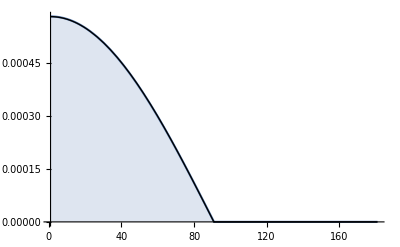

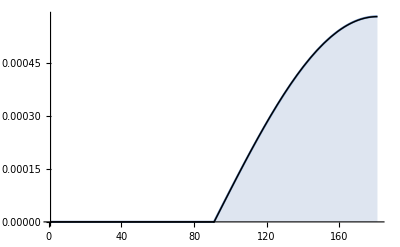

```mathematica
Show[DiscretePlot[delays[[All,1]][[k]],{k,1,n}],Plot[fun1,{x,1,n},PlotStyle->{Thick,Black}]]
Show[DiscretePlot[delays[[All,2]][[k]],{k,1,n}],Plot[fun2,{x,1,n},PlotStyle->{Thick,Black}]]
```

```mathematica
1+180*V/Vmax
```

1+(180 V)/Vmax